## Spectrum

-Graphics3D-

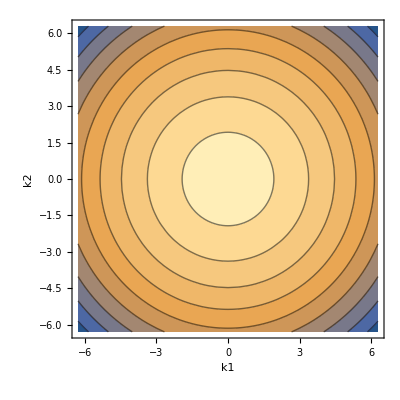

```mathematica
Hamiltonian[k1_,k2_,M_,A_,B_,C_,D_]:=A*k1*PauliMatrix[1]+A*k2*PauliMatrix[2]+(M-B*(k1^2+k2^2))*PauliMatrix[3]+(C-D*(k1^2+k2^2))*IdentityMatrix[2];
Htop[k1_,k2_,M_,A_,B_,C_,D_]:=Hamiltonian[k1,k2,M,A,B,C,D];
Hbot[k1_,k2_,M_,A_,B_,C_,D_]:=Conjugate[Hamiltonian[-k1,-k2,M,A,B,C,D]];
Heff[k1_,k2_,M_,A_,B_,C_,D_]:=ArrayFlatten[{{Htop[k1,k2,M,A,B,C,D],0},{0,Hbot[k1,k2,M,A,B,C,D]}}];
Energy[k1_,k2_,M_,A_,B_,C_,D_]:=Eigenvalues[Hamiltonian[k1,k2,M,A,B,C,D]];
(*Energy[1,1,1,1,1,1,1]*)
Plot3D[Energy[k1,k2,3,5,1,0,0.1],{k1,-2*Pi,2*Pi},{k2,-2*Pi,2*Pi},AxesLabel->Automatic, BoxRatios->{1, 1, 1}]
ContourPlot[Energy[k1,k2,3,5,1,0,0.1][[1]],{k1,-2*Pi,2*Pi},{k2,-2*Pi,2*Pi},AxesLabel->Automatic, BoxRatios->{1, 1}]
```

Contour plot is only for top energy level (if it were both it would just be constant).

## Spectrum of “full” model

```mathematica
FullHamiltonian[k1_,k2_,M_,A_,B_,C_,D_]:=A*Sin[k1]*PauliMatrix[1]+A*Sin[k2]*PauliMatrix[2]+(-2*B*(2−M/(2*B)-Cos[k1]-Cos[k2]))*PauliMatrix[3]+(C-2*D*(2-Cos[k1]+Cos[k2]))*IdentityMatrix[2];
FullEnergy[k1_,k2_,M_,A_,B_,C_,D_]:=Eigenvalues[FullHamiltonian[k1,k2,M,A,B,C,D]];
FullHamiltonian[k1,k2,M,A,B,C,D] // MatrixForm
```

(C-2 B (2-M/(2 B)-Cos[k1]-Cos[k2])-2 D (2-Cos[k1]+Cos[k2]) | A Sin[k1]-ⅈ A Sin[k2]
A Sin[k1]+ⅈ A Sin[k2] | C+2 B (2-M/(2 B)-Cos[k1]-Cos[k2])-2 D (2-Cos[k1]+Cos[k2]))

-Graphics3D-

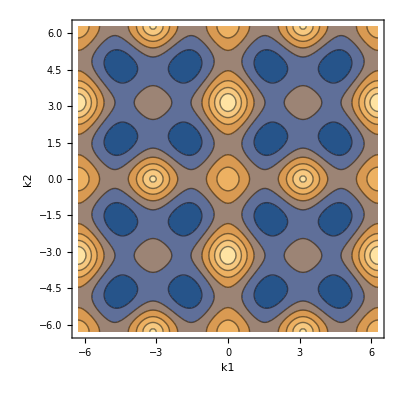

```mathematica
Plot3D[FullEnergy[k1,k2,3,5,1,0,0.1],{k1,-2*Pi,2*Pi},{k2,-2*Pi,2*Pi},AxesLabel->Automatic, BoxRatios->{1, 1, 1}]
ContourPlot[FullEnergy[k1,k2,3,5,1,0,0.1][[1]],{k1,-2*Pi,2*Pi},{k2,-2*Pi,2*Pi},AxesLabel->Automatic, BoxRatios->{1, 1}]
```

Are both models the same in a small k region? Take the top layer and check.

```mathematica
FullEnergy[0,0,3,5,1,0,0.1]
```

{-3.4,2.6}

```mathematica
Efull[k1_,k2_]:= FullEnergy[k1,k2,3,5,1,0,0.1][[1]];
Elin[k1_,k2_]:= Energy[k1,k2,3,5,1,0,0.1][[1]];
DelE[k1_,k2_]:=Abs[Efull[k1,k2] -Elin[k1,k2]];
Plot3D[DelE[k1,k2],{k1,-0.5,0.5},{k2,-0.5,0.5}]
```

-Graphics3D-

The relative error is quite large. Compute.

```mathematica
MaxError=NMaxValue[DelE[k1,k2],{k1,k2}∈ Disk[]];
RelError=N[DelE[0,0]/Efull[0,0]]
```

-3.09091

## Real-space model